# Model to describe the efficiency as a function of mass and ctau

```mathematica
f1[m_,E_,ct_,R_,z_]:=R/(2(E/m)ct(R^2+z^2))(Exp[(-√(R^2+z^2))/((E/m)ct)])  (* Exponencial decay of the GammaD *)
```

```mathematica
Zmax[m_,E_,ct_,R_]:= If[10.0 (E/m) ct<(10 R),10 (E/m) ct,10 R]
```

```mathematica
effR[R0_,R_]:= Which[R>0&&R<R0,1.0,R>R0,0.0] (* efficiency 1 before R0=9.8cm (3rd pixel layer) and zero above this value *)
```

```mathematica
Rmax[m_,E_,ct_]:=Which[10(E/m)ct<600,10(E/m)ct,10(E/m)ct≥600,600.0]
```

```mathematica
alpha0[m_]:=Which[m==0.25,0.0235,m==0.4,0.0198,m==0.7,0.019,m==1.0,0.0195,m==2.0,0.0189,m==5.0,0.0184,m==8.5,0.0184,m==15,0.0177,m==25,0.0219,m==35,0.0478,m==58,0.202] (*Efficiencies for ctau=0*)
```

```mathematica
datapoints= {{0.25,alpha0[0.25]},{0.4,0.06951},{0.7,alpha0[0.7]},{1.0,alpha0[1.0]},{2.0,alpha0[2.0]},{5.0,alpha0[5.0]},{8.5,alpha0[8.5]},{15.0,alpha0[15.0]},{25.0,alpha0[25.0]},{35.0,alpha0[35.0]},{58.0,alpha0[58.0]}};
```

```mathematica
feffR=Interpolation[datapoints,InterpolationOrder->1];
```

```mathematica
f3[m_,E_,ct_]:=NIntegrate[effR[160.0,R]2f1[m,E,ct,R,z],{R,0.0,Rmax[m,E,ct]},{z,0.0,Zmax[m,E,ct,R]}]
```

```mathematica
alphavsctau[m_,E_,ct_]:=feffR[m] f3[m,E,ct] f3[m,E,ct]  (* Final expression of the model with to variables m and ctau, the Energy for the GamamD = 50 GeV which is mean value of distribution *)
```

### Calling external data for limit setting (Br, limit on N, f(m), etc...)

```mathematica
(* Model Independent Limit *)
```

```mathematica
Nlimit = ReadList["/Users/alfre/Documents/GitHub/MuJetAnalysis_LimitsPlotting/scripts/Nlimit_observed.dat",{Real,Real}]; (* Br  GammaD to 2 mu *)
```

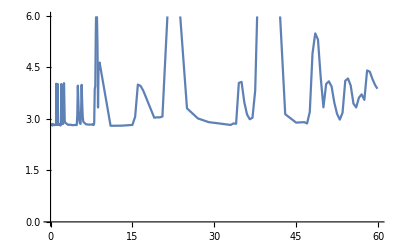

```mathematica
ListPlot[Nlimit,Joined->True]
```

```mathematica
Nlimitf = Interpolation[Nlimit,InterpolationOrder->1]
```

InterpolatingFunction[{{0.2113, 59.9}}, <>]

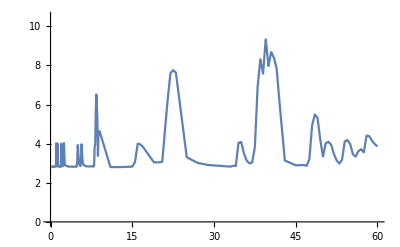

```mathematica
Plot[Nlimitf[m],{m,0.25,60.0},PlotRange->{{0.0,60.0},{0.0,10.5}}]
```

```mathematica
(*Nlimitf[x_]:=2.4+0.196258*Exp[-0.5*((x-0.585342)/0.0400199)^2]+1.32241*Exp[-0.5*((x-0.833146)/0.0350001)^2]+0.893637*Exp[-0.5*((x-1.16449)/0.033)^2]+1.79953*Exp[-0.5*((x-1.41323)/0.03)^2]+0.59907*Exp[-0.5*((x-1.90641)/0.05)^2]+1.1*Exp[-0.5*((x-2.40133)/0.042)^2]+2.20401*Exp[-0.5*((x-2.999)/0.169458)^2]+3.57*Exp[-0.5*((x-3.1005)/0.134076)^2]*)
(*Nlimitf[x_]:= 3.09*)
```

```mathematica
Br = ReadList["/Users/alfre/Documents/GitHub/MuJetAnalysis_LimitsPlotting/scripts/Br_2018.dat",{Real,Real}]; (* Br  GammaD to 2 mu *)
```

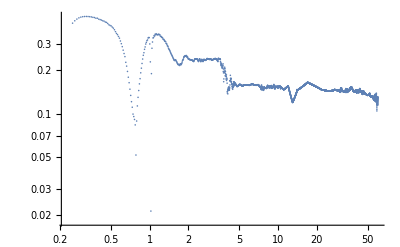

```mathematica
ListLogLogPlot[Br]
```

```mathematica
Brf = Interpolation[Br,InterpolationOrder->1]
```

InterpolatingFunction[{{0.25, 59.99}}, <>]

```mathematica
listBrf = Table[{m,Brf[m]},{m,0.0,60.0,0.01}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

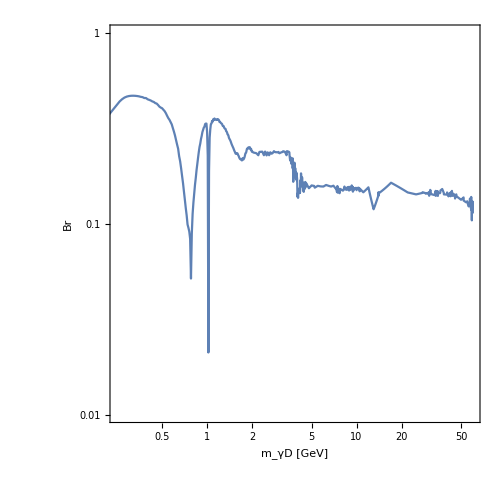

```mathematica
Brlog=ListLogLogPlot[listBrf,Joined->True,Joined->True,ImageSize->500,AspectRatio->1.0,TicksStyle->Directive[FontSize->16],Frame->True,FrameLabel->{"m_γD [GeV]","Br"},RotateLabel->True,BaseStyle->{FontSize->20},PlotRange->{{0.25,60.0},{0.01,1.0}}]
```

```mathematica
fm = ReadList["/Users/alfre/Documents/GitHub/MuJetAnalysis_LimitsPlotting/scripts/fm_2018.dat",{Real,Real}]; (* Br  GammaD to 2 mu *)
```

```mathematica
fmf = Interpolation[fm,InterpolationOrder->1]
```

InterpolatingFunction[{{0.25, 59.99}}, <>]

```mathematica
fmf[1.0]
```

124.279

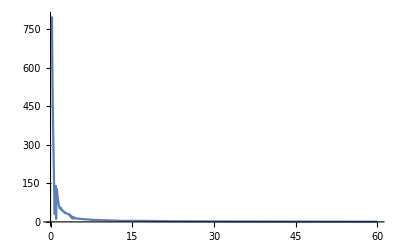

```mathematica
Plot[fmf[m],{m,0.25,60.0},PlotRange->{{0.0,60.0},{0.0,800}}]
```

#### Limit on Br(H→2γ) as a function of mass and ctau for different values (1%, 5%,10%,20%,40%)

```mathematica
(* Since we have epsilon as a function of the mass and ctau we cannot just plot the distributions as above, the limit is done in an iterative way getting the value in every mass bin and scanning in epsilon until it converges to the value of 3.07*)
```

```mathematica
ctauval[m_] := (1.97×10^-13 fmf[m])/10^Mineps2;  (* since our efficiency model is expresed in terms of ctau we need to correlate to which epsilon variable it correspond, at this step using epsilon^2 to avoid the sqrt *)
Nlimit2[m_,BrHtoGam_]:= 59.7 * 61000* BrHtoGam *  alphavsctau[m,50,ctauval[m]]* Brf[m] * Brf[m]; (*Higgs total cross seciton https://www.sciencedirect.com/science/article/pii/S037026931930228X *)(* This is the expression for the limit this expresion will be evaluated in the mass and ctau space until it converges to a value close to the limit on N(m) *)
```

```mathematica
Labelepsvsctau={"cτ=100.0","cτ=50.0","cτ=20.0","cτ=10.0","cτ=5.0","cτ=3.0","cτ=1.0","cτ=0.1","cτ=0.001","cτ=0.00001"}
```

{cτ=100.0,cτ=50.0,cτ=20.0,cτ=10.0,cτ=5.0,cτ=3.0,cτ=1.0,cτ=0.1,cτ=0.001,cτ=0.00001}

#### Br=0.1%

#### Br=1%

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.01; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,2.72};
step={0.1,0.1,0.1,0.05,0.05,0.05};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5(*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,6,1}];
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_m0to60_observed_part1.dat",listbr1];
```

{{Null,Null}}

{1.04083×10^-17,0.25,-10.61,2.92745}

{0.08,0.3,-10.98,2.89975}

{0.06,0.35,-11.21,2.99808}

{0.09,0.4,-11.4,2.91789}

{0.03,0.45,-11.48,2.8818}

{0.01,0.5,-11.54,2.86346}

{0.05,0.55,-11.58,2.86041}

{0.09,0.6,-11.6,2.84834}

{0.05,0.65,-11.58,2.89084}

{0.06,0.7,-11.49,2.86454}

{0.06,0.7,-11.49,2.86454}

{0.08,0.75,-11.43,2.85515}

{0.04,0.8,-11.55,2.83878}

{0.09,0.85,-11.7,2.90459}

{0.09,0.85,-11.7,2.90459}

{0.08,0.9,-11.79,2.84988}

{0.07,0.95,-11.84,2.99876}

{0.08,1.,-11.88,3.02189}

{0.08,1.,-11.88,3.02189}

{0.01,1.01,-11.86,3.05718}

{0.09,1.02,-4.,0.315796}

{0.04,1.03,-11.85,3.10378}

{0.09,1.04,-11.9,3.1225}

{0.06,1.05,-11.91,3.19735}

{0.01,1.06,-11.86,4.09173}

{1.04083×10^-17,1.07,-11.87,4.07049}

{0.08,1.08,-11.88,4.0766}

{0.08,1.09,-11.88,4.19527}

{0.09,1.1,-11.9,4.03612}

{0.06,1.11,-11.91,3.98931}

{1.04083×10^-17,1.12,-11.93,3.82083}

{0.05,1.13,-11.94,3.77409}

{0.03,1.14,-11.96,3.59019}

{0.08,1.15,-11.97,3.55109}

{0.06,1.16,-11.98,3.51841}

{0.09,1.17,-12.,3.35241}

{0.01,1.18,-12.02,3.17979}

{0.03,1.19,-12.04,3.02348}

{0.06,1.2,-12.05,2.9839}

{0.06,1.2,-12.05,2.9839}

{0.08,1.21,-12.06,2.9338}

{0.08,1.22,-12.06,3.01876}

{0.07,1.23,-12.08,2.85907}

{0.07,1.24,-12.08,2.9338}

{0.07,1.25,-12.08,3.01361}

{0.09,1.26,-12.1,2.8539}

{0.09,1.27,-12.1,2.91721}

{0.07,1.28,-12.08,3.23961}

{0.02,1.29,-12.03,4.04321}

{0.02,1.3,-12.03,4.12389}

{0.03,1.31,-12.04,4.05758}

{0.03,1.32,-12.04,4.1554}

{0.06,1.33,-12.05,4.09503}

{0.08,1.34,-12.06,4.00437}

{0.09,1.35,-12.1,3.51308}

{0.06,1.36,-12.12,3.31901}

{0.06,1.37,-12.12,3.37649}

{0.01,1.38,-12.14,3.19754}

{0.08,1.39,-12.15,3.13675}

{0.07,1.4,-12.16,3.06676}

{0.05,1.41,-12.18,2.8954}

{0.05,1.42,-12.18,2.9549}

{0.06,1.43,-12.19,2.89967}

{0.06,1.44,-12.19,2.95387}

{0.09,1.45,-12.2,2.89227}

{0.09,1.46,-12.2,2.9436}

{0.09,1.47,-12.2,2.99678}

{0.02,1.48,-12.21,2.93721}

{0.02,1.49,-12.21,2.98943}

{0.01,1.5,-12.22,2.92994}

{0.01,1.51,-12.22,2.97821}

{0.01,1.52,-12.22,3.02718}

{0.08,1.53,-12.24,2.8555}

{0.08,1.54,-12.24,2.90411}

{0.08,1.55,-12.24,2.94905}

{0.08,1.56,-12.24,3.00679}

{0.06,1.57,-12.26,2.85479}

{0.06,1.58,-12.26,2.91696}

{0.06,1.59,-12.26,2.97425}

{0.06,1.6,-12.26,3.02881}

{0.03,1.61,-12.28,2.85056}

{0.03,1.62,-12.28,2.8996}

{0.03,1.63,-12.28,2.94423}

{0.03,1.64,-12.28,2.98323}

{0.03,1.65,-12.28,3.03262}

{0.09,1.66,-12.3,2.8595}

{0.09,1.67,-12.3,2.91242}

{0.09,1.68,-12.3,2.96915}

{0.09,1.69,-12.3,3.02196}

{0.07,1.7,-12.32,2.84922}

{0.07,1.71,-12.32,2.89695}

{0.08,1.72,-12.33,2.8592}

{0.08,1.73,-12.33,2.92964}

{0.08,1.74,-12.33,2.97669}

{0.08,1.75,-12.33,3.01557}

{0.04,1.76,-12.35,2.86392}

{0.05,1.77,-12.36,2.8177}

{0.05,1.78,-12.36,2.88217}

{0.05,1.79,-12.36,2.95312}

{0.01,1.8,-12.38,2.81341}

{0.01,1.81,-12.38,2.87549}

{0.02,1.82,-12.39,2.82147}

{0.02,1.83,-12.39,2.88563}

{0.09,1.84,-12.4,2.85076}

{0.09,1.85,-12.4,2.91736}

{0.09,1.86,-12.4,2.9674}

{1.04083×10^-17,1.87,-12.41,2.90695}

{0.08,1.88,-12.42,2.86014}

{0.08,1.89,-12.42,2.91304}

{0.08,1.9,-12.42,2.95335}

{0.08,1.91,-12.42,3.00378}

{0.03,1.92,-12.44,2.83953}

{0.08,1.93,-12.42,3.1189}

{0.09,1.94,-12.4,3.40636}

{0.05,1.95,-12.36,3.98055}

{0.05,1.96,-12.36,4.04724}

{0.05,1.97,-12.36,4.11807}

{0.05,1.98,-12.36,4.1532}

{0.05,1.99,-12.36,4.18976}

{1.04083×10^-17,2.,-12.37,4.10864}

{1.04083×10^-17,2.,-12.37,4.10864}

{0.01,2.01,-12.38,4.01892}

{0.09,2.02,-12.4,3.79128}

{0.03,2.03,-12.44,3.32234}

{0.04,2.04,-12.45,3.24882}

{0.04,2.05,-12.45,3.29862}

{0.06,2.06,-12.47,3.11051}

{0.07,2.07,-12.48,3.04302}

{0.07,2.08,-12.48,3.08936}

{0.07,2.09,-12.48,3.13606}

{0.09,2.1,-12.5,2.95544}

{0.09,2.11,-12.5,2.99993}

{0.09,2.12,-12.5,3.04476}

{0.09,2.13,-12.5,3.08994}

{0.08,2.14,-12.51,3.01992}

{0.08,2.15,-12.51,3.06081}

{0.03,2.16,-12.52,2.98913}

{0.03,2.17,-12.52,3.02917}

{0.03,2.18,-12.52,3.0694}

{0.06,2.19,-12.54,2.88801}

{0.06,2.2,-12.54,2.92624}

{0.06,2.21,-12.54,2.98071}

{0.06,2.22,-12.54,3.03611}

{0.07,2.23,-12.56,2.87038}

{0.07,2.24,-12.56,2.92265}

{0.07,2.25,-12.56,2.96535}

{0.07,2.26,-12.56,3.00842}

{0.07,2.27,-12.56,3.05186}

{0.02,2.28,-12.57,2.98241}

{0.02,2.29,-12.57,3.02514}

{0.01,2.3,-12.58,2.95584}

{0.01,2.31,-12.58,2.99787}

{0.01,2.32,-12.58,3.04025}

{0.01,2.33,-12.58,3.08297}

{0.01,2.34,-12.58,3.12558}

{0.01,2.35,-12.58,3.15956}

{1.04083×10^-17,2.36,-12.59,3.07751}

{1.04083×10^-17,2.37,-12.59,3.11061}

{0.09,2.38,-12.6,3.02966}

{0.09,2.39,-12.6,3.0619}

{0.09,2.4,-12.6,3.09412}

{0.07,2.41,-12.56,3.64325}

{0.06,2.42,-12.54,3.98416}

{0.06,2.43,-12.54,4.05487}

{0.06,2.44,-12.54,4.12682}

{0.06,2.45,-12.54,4.17762}

{0.06,2.46,-12.54,4.21291}

{0.04,2.47,-12.55,4.09966}

{0.04,2.48,-12.55,4.1339}

{0.07,2.49,-12.56,4.02275}

{0.02,2.5,-12.57,3.91449}

{0.01,2.51,-12.58,3.83947}

{0.09,2.52,-12.6,3.63162}

{0.09,2.53,-12.6,3.69129}

{0.06,2.54,-12.61,3.61819}

{0.02,2.55,-12.63,3.40188}

{0.07,2.56,-12.64,3.31149}

{0.07,2.57,-12.64,3.34379}

{0.05,2.58,-12.66,3.13729}

{0.05,2.59,-12.66,3.16796}

{0.06,2.6,-12.68,2.97158}

{0.06,2.61,-12.68,3.0179}

{0.08,2.62,-12.69,2.95333}

{0.08,2.63,-12.69,2.99922}

{0.09,2.64,-12.7,2.9344}

{0.09,2.65,-12.7,2.97287}

{0.09,2.66,-12.7,3.00514}

{0.09,2.67,-12.7,3.03751}

{0.09,2.68,-12.7,3.07}

{1.04083×10^-17,2.69,-12.71,2.98969}

{0.07,2.7,-12.72,2.91123}

{0.07,2.71,-12.72,2.9478}

{0.07,2.72,-12.72,2.98467}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.01; (* value of Br(H->GammaD) *)
min= {3.24}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={9.0};
step={0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_m0to60_observed_part2.dat",listbr1];
```

{{Null,Null}}

{0.08,3.24,-12.87,3.02203}

{0.09,3.34,-12.9,2.95888}

{0.09,3.44,-12.9,3.27462}

{0.08,3.54,-12.96,2.8593}

{0.08,3.64,-12.96,3.00522}

{0.08,3.74,-12.96,3.12536}

{0.09,3.84,-13.,3.03156}

{0.09,3.94,-13.,3.05587}

{0.09,4.04,-13.,2.85641}

{0.09,4.14,-13.,3.20475}

{0.08,4.24,-13.05,3.06788}

{0.08,4.34,-13.05,3.2585}

{0.08,4.44,-13.05,3.27153}

{0.09,4.54,-13.1,3.1367}

{0.09,4.64,-13.1,3.28003}

{0.08,4.74,-13.14,3.00251}

{0.08,4.84,-13.14,3.15874}

{0.09,4.94,-13.1,3.82112}

{0.09,5.04,-13.1,4.05145}

{0.08,5.14,-13.14,3.76943}

{0.09,5.24,-13.2,3.25352}

{0.08,5.34,-13.23,3.12275}

{0.08,5.44,-13.23,3.30562}

{0.08,5.54,-13.23,3.48448}

{0.09,5.64,-13.2,4.00241}

{0.09,5.74,-13.2,4.18221}

{0.07,5.84,-13.28,3.4249}

{0.09,5.94,-13.3,3.36725}

{0.08,6.04,-13.32,3.31462}

{0.07,6.14,-13.36,3.06596}

{0.07,6.24,-13.36,3.22307}

{0.09,6.34,-13.4,2.95482}

{0.09,6.44,-13.4,3.08105}

{0.09,6.54,-13.4,3.20931}

{0.09,6.64,-13.4,3.33982}

{0.07,6.74,-13.44,3.05667}

{0.07,6.84,-13.44,3.19152}

{0.07,6.94,-13.44,3.33097}

{0.09,7.04,-13.5,2.85068}

{0.09,7.14,-13.5,2.94303}

{0.09,7.24,-13.5,3.03472}

{0.09,7.34,-13.5,3.11468}

{0.09,7.44,-13.5,3.3321}

{0.09,7.54,-13.5,3.32462}

{0.07,7.64,-13.52,3.25131}

{0.07,7.74,-13.52,3.33955}

{0.05,7.84,-13.56,3.10596}

{0.08,7.94,-13.59,2.91074}

{0.07,8.04,-13.52,3.73036}

{0.09,8.14,-13.5,4.08492}

{0.07,8.24,-13.44,5.0756}

{0.06,8.34,-13.38,6.15404}

{0.07,8.44,-13.36,6.53803}

{0.09,8.54,-13.4,6.07919}

{0.09,8.64,-13.5,4.79632}

{0.08,8.74,-13.59,3.83866}

{0.07,8.84,-13.52,4.77125}

{0.07,8.94,-13.52,4.95837}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.01; (* value of Br(H->GammaD) *)
min= {11.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={60};
step={0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_m0to60_observed_part3.dat",listbr1];
```

{{Null,Null}}

{0.08,11.,-13.86,2.949}

{0.08,11.1,-13.86,3.00919}

{0.08,11.2,-13.86,3.09418}

{0.09,11.3,-13.9,2.80412}

{0.09,11.4,-13.9,2.88327}

{0.09,11.5,-13.9,2.96395}

{0.09,11.6,-13.9,3.04616}

{0.09,11.7,-13.9,3.12994}

{0.09,11.8,-13.9,3.21531}

{0.08,11.9,-13.95,2.81499}

{0.08,12.,-13.95,2.89205}

{0.08,12.1,-13.95,2.90554}

{0.08,12.2,-13.95,2.91728}

{0.08,12.3,-13.95,2.92729}

{0.08,12.4,-13.95,2.93556}

{0.08,12.5,-13.95,2.9421}

{0.08,12.6,-13.95,2.94694}

{0.08,12.7,-13.95,2.95009}

{0.08,12.8,-13.95,2.95158}

{0.08,12.9,-13.95,2.95142}

{0.08,13.,-13.95,2.94965}

{0.08,13.1,-13.95,3.04028}

{0.08,13.2,-13.95,3.13389}

{0.08,13.3,-13.95,3.23059}

{0.09,13.4,-14.,2.89098}

{0.09,13.5,-14.,2.98033}

{0.09,13.6,-14.,3.07266}

{0.09,13.7,-14.,3.16808}

{0.09,13.8,-14.,3.26673}

{0.08,13.9,-14.04,2.99122}

{0.08,14.,-14.04,3.0844}

{0.08,14.1,-14.04,3.19546}

{0.08,14.2,-14.04,3.26271}

{0.07,14.3,-14.08,2.94577}

{0.09,14.4,-14.1,2.82518}

{0.09,14.5,-14.1,2.88508}

{0.09,14.6,-14.1,2.94576}

{0.09,14.7,-14.1,3.00725}

{0.09,14.8,-14.1,3.06954}

{0.09,14.9,-14.1,3.13263}

{0.09,15.,-14.1,3.19654}

{0.09,15.1,-14.1,3.27101}

{0.09,15.2,-14.1,3.3467}

{0.09,15.3,-14.1,3.42365}

{0.09,15.4,-14.1,3.50186}

{0.08,15.5,-14.13,3.26433}

{0.09,15.6,-14.1,3.66213}

{0.09,15.7,-14.1,3.74422}

{0.09,15.8,-14.1,3.82764}

{0.09,15.9,-14.1,3.91241}

{0.07,16.,-14.08,4.24382}

{0.09,16.1,-14.1,4.08606}

{0.09,16.2,-14.1,4.17497}

{0.09,16.3,-14.1,4.2653}

{0.09,16.4,-14.1,4.35707}

{0.09,16.5,-14.1,4.45029}

{0.08,16.6,-14.13,4.15514}

{0.08,16.7,-14.13,4.24418}

{0.08,16.8,-14.13,4.33465}

{0.07,16.9,-14.16,4.04031}

{0.07,17.,-14.16,4.12655}

{0.07,17.1,-14.16,4.19401}

{0.09,17.2,-14.2,3.76569}

{0.09,17.3,-14.2,3.8282}

{0.09,17.4,-14.2,3.89102}

{0.09,17.5,-14.2,3.95415}

{0.09,17.6,-14.2,4.01757}

{0.08,17.7,-14.22,3.83645}

{0.08,17.8,-14.22,3.89778}

{0.08,17.9,-14.22,3.95939}

{0.07,18.,-14.24,3.77962}

{0.07,18.1,-14.24,3.83918}

{0.05,18.2,-14.28,3.43818}

{0.06,18.3,-14.29,3.38347}

{0.09,18.4,-14.3,3.3292}

{0.09,18.5,-14.3,3.38231}

{0.09,18.6,-14.3,3.43572}

{0.09,18.7,-14.3,3.48941}

{0.09,18.8,-14.3,3.54337}

{0.08,18.9,-14.31,3.4858}

{0.07,19.,-14.32,3.42873}

{0.07,19.1,-14.32,3.48109}

{0.07,19.2,-14.32,3.53371}

{0.06,19.3,-14.36,3.1572}

{0.06,19.4,-14.36,3.20568}

{0.06,19.5,-14.36,3.25441}

{0.06,19.6,-14.36,3.30341}

{0.06,19.7,-14.36,3.35265}

{0.06,19.8,-14.36,3.40214}

{0.06,19.9,-14.36,3.45187}

{0.09,20.,-14.4,3.08203}

{0.09,20.1,-14.4,3.12782}

{0.09,20.2,-14.4,3.17385}

{0.09,20.3,-14.4,3.22011}

{0.09,20.4,-14.4,3.26661}

{0.09,20.5,-14.4,3.31333}

{0.06,20.6,-14.36,3.80605}

{0.06,20.7,-14.36,3.85743}

{0.08,20.8,-14.31,4.53467}

{0.09,20.9,-14.3,4.72528}

{0.09,21.,-14.3,4.78314}

{0.05,21.1,-14.28,5.11995}

{0.07,21.2,-14.24,5.76966}

{0.07,21.3,-14.24,5.83271}

{0.08,21.4,-14.22,6.207}

{0.09,21.5,-14.2,6.59183}

{0.09,21.6,-14.2,6.65702}

{0.02,21.7,-14.19,6.88607}

{0.07,21.8,-14.16,7.45406}

{0.07,21.9,-14.16,7.51993}

{0.06,22.,-14.15,7.75795}

{0.07,22.1,-14.16,7.66373}

{0.07,22.2,-14.16,7.74024}

{0.07,22.3,-14.16,7.81669}

{0.07,22.4,-14.16,7.89307}

{0.07,22.5,-14.16,7.96938}

{0.07,22.6,-14.16,8.0456}

{0.07,22.7,-14.16,8.12172}

{0.01,22.8,-14.18,7.85104}

{0.02,22.9,-14.19,7.75367}

{0.09,23.,-14.2,7.65629}

{0.09,23.1,-14.2,7.73013}

{0.08,23.2,-14.22,7.46161}

{0.07,23.3,-14.24,7.19588}

{0.07,23.4,-14.24,7.26722}

{0.05,23.5,-14.28,6.67453}

{0.09,23.6,-14.3,6.41969}

{0.09,23.7,-14.3,6.48668}

{0.08,23.8,-14.31,6.39323}

{0.05,23.9,-14.34,5.9872}

{0.06,24.,-14.36,5.7447}

{0.02,24.1,-14.37,5.65603}

{0.09,24.2,-14.4,5.27553}

{0.06,24.3,-14.43,4.91044}

{0.06,24.4,-14.43,4.96635}

{0.05,24.5,-14.46,4.61446}

{0.08,24.6,-14.49,4.27906}

{0.09,24.7,-14.5,4.20394}

{0.05,24.8,-14.52,4.00802}

{0.07,24.9,-14.56,3.5911}

{0.08,25.,-14.58,3.41588}

{0.08,25.1,-14.58,3.49554}

{0.09,25.2,-14.6,3.35836}

{0.09,25.3,-14.6,3.43582}

{0.09,25.4,-14.6,3.51437}

{0.09,25.5,-14.6,3.59402}

{0.09,25.6,-14.6,3.67478}

{0.07,25.7,-14.64,3.30803}

{0.07,25.8,-14.64,3.38212}

{0.07,25.9,-14.64,3.45724}

{0.08,26.,-14.67,3.206}

{0.08,26.1,-14.67,3.27676}

{0.08,26.2,-14.67,3.34851}

{0.08,26.3,-14.67,3.42124}

{0.09,26.4,-14.7,3.16717}

{0.09,26.5,-14.7,3.23556}

{0.09,26.6,-14.7,3.3049}

{0.09,26.7,-14.7,3.37518}

{0.09,26.8,-14.7,3.44642}

{0.09,26.9,-14.7,3.51862}

{0.07,27.,-14.72,3.36241}

{0.07,27.1,-14.72,3.43227}

{0.08,27.2,-14.76,3.06329}

{0.08,27.3,-14.76,3.12682}

{0.08,27.4,-14.76,3.1912}

{0.08,27.5,-14.76,3.25645}

{0.08,27.6,-14.76,3.33102}

{0.08,27.7,-14.76,3.4023}

{0.09,27.8,-14.8,3.02565}

{0.09,27.9,-14.8,3.08417}

{0.09,28.,-14.8,3.14338}

{0.09,28.1,-14.8,3.20328}

{0.09,28.2,-14.8,3.26387}

{0.09,28.3,-14.8,3.32515}

{0.09,28.4,-14.8,3.38714}

{0.05,28.5,-14.82,3.22171}

{0.08,28.6,-14.85,2.95738}

{0.08,28.7,-14.85,3.01239}

{0.08,28.8,-14.85,3.06803}

{0.08,28.9,-14.85,3.12431}

{0.08,29.,-14.85,3.17216}

{0.08,29.1,-14.85,3.23151}

{0.08,29.2,-14.85,3.2916}

{0.08,29.3,-14.85,3.35242}

{0.07,29.4,-14.88,3.07639}

{0.09,29.5,-14.9,2.92036}

{0.09,29.6,-14.9,2.97415}

{0.09,29.7,-14.9,3.02862}

{0.09,29.8,-14.9,3.08374}

{0.09,29.9,-14.9,3.13954}

{0.09,30.,-14.9,3.19602}

{0.09,30.1,-14.9,3.25317}

{0.09,30.2,-14.9,3.31778}

{0.08,30.3,-14.94,2.9369}

{0.08,30.4,-14.94,2.96258}

{0.08,30.5,-14.94,3.00123}

{0.08,30.6,-14.94,3.03998}

{0.08,30.7,-14.94,3.1094}

{0.08,30.8,-14.94,3.18385}

{0.08,30.9,-14.94,3.26005}

{0.08,31.,-14.94,3.33805}

{0.07,31.1,-14.96,3.18182}

{0.07,31.2,-14.96,3.22883}

{0.07,31.3,-14.96,3.25243}

{0.07,31.4,-14.96,3.29287}

{0.09,31.5,-15.,2.88894}

{0.09,31.6,-15.,2.92885}

{0.09,31.7,-15.,2.97668}

{0.09,31.8,-15.,3.02502}

{0.09,31.9,-15.,3.07386}

{0.09,32.,-15.,3.12321}

{0.09,32.1,-15.,3.17307}

{0.09,32.2,-15.,3.22343}

{0.09,32.3,-15.,3.27432}

{0.09,32.4,-15.,3.32571}

{0.08,32.5,-15.03,3.0335}

{0.08,32.6,-15.03,3.08111}

{0.08,32.7,-15.03,3.12919}

{0.08,32.8,-15.03,3.17777}

{0.08,32.9,-15.03,3.22683}

{0.08,33.,-15.03,3.27638}

{0.08,33.1,-15.03,3.32642}

{0.07,33.2,-15.04,3.25816}

{0.07,33.3,-15.04,3.31667}

{0.06,33.4,-15.06,3.14104}

{0.06,33.5,-15.06,3.19715}

{0.06,33.6,-15.06,3.2541}

{0.06,33.7,-15.06,3.3119}

{0.09,33.8,-15.1,2.93109}

{0.09,33.9,-15.1,2.9054}

{0.09,34.,-15.1,2.95581}

{0.06,34.1,-15.06,3.47602}

{0.07,34.2,-15.04,3.79767}

{0.08,34.3,-15.03,4.00238}

{0.08,34.4,-15.03,4.07134}

{0.08,34.5,-15.03,4.14132}

{0.08,34.6,-15.03,4.24067}

{0.08,34.7,-15.03,4.21879}

{0.08,34.8,-15.03,4.34228}

{0.08,34.9,-15.03,4.3964}

{0.08,35.,-15.03,4.37772}

{0.07,35.1,-15.04,4.38965}

{0.06,35.2,-15.06,4.18394}

{0.03,35.3,-15.08,3.98463}

{0.09,35.4,-15.1,3.79181}

{0.09,35.5,-15.1,3.87669}

{0.08,35.6,-15.12,3.68515}

{0.08,35.7,-15.12,3.76609}

{0.06,35.8,-15.13,3.71036}

{0.04,35.9,-15.15,3.52256}

{0.05,36.,-15.18,3.21981}

{0.05,36.1,-15.18,3.28883}

{0.09,36.2,-15.2,3.12073}

{0.09,36.3,-15.2,3.19081}

{0.09,36.4,-15.2,3.28868}

{0.09,36.5,-15.2,3.35939}

{0.09,36.6,-15.2,3.43107}

{0.09,36.7,-15.2,3.50372}

{0.08,36.8,-15.21,3.4451}

{0.08,36.9,-15.21,3.51705}

{0.05,37.,-15.24,3.20382}

{0.08,37.1,-15.21,3.66386}

{0.08,37.2,-15.21,3.73874}

{0.09,37.3,-15.2,3.96055}

{0.09,37.4,-15.2,4.04026}

{0.09,37.5,-15.2,4.11041}

{0.05,37.6,-15.18,4.50341}

{0.06,37.7,-15.13,5.49479}

{0.08,37.8,-15.12,5.78822}

{0.09,37.9,-15.1,6.31352}

{0.06,38.,-15.06,7.36991}

{0.06,38.1,-15.06,7.48245}

{0.06,38.2,-15.06,7.5956}

{0.04,38.3,-15.05,7.97576}

{0.07,38.4,-15.04,8.30055}

{0.08,38.5,-15.03,8.72745}

{0.07,38.6,-15.04,8.58507}

{0.06,38.7,-15.06,8.16418}

{0.06,38.8,-15.06,8.30133}

{0.03,38.9,-15.08,7.88802}

{0.03,39.,-15.08,8.0195}

{0.03,39.1,-15.08,8.15226}

{1.04083×10^-17,39.2,-15.07,8.57088}

{0.06,39.3,-15.06,9.00717}

{0.06,39.4,-15.06,9.15239}

{0.04,39.5,-15.05,9.61264}

{0.06,39.6,-15.06,9.44693}

{0.03,39.7,-15.08,8.97601}

{0.02,39.8,-15.09,8.81582}

{0.09,39.9,-15.1,8.6566}

{0.08,40.,-15.12,8.21239}

{0.08,40.1,-15.12,8.34132}

{0.08,40.2,-15.12,8.47147}

{0.08,40.3,-15.12,8.60284}

{0.08,40.4,-15.12,8.83709}

{0.08,40.5,-15.12,8.94749}

{0.08,40.6,-15.12,9.05828}

{0.06,40.7,-15.13,8.86138}

{0.06,40.8,-15.13,8.97005}

{0.04,40.9,-15.15,8.47719}

{0.04,41.,-15.15,8.58097}

{0.04,41.1,-15.15,8.68514}

{0.03,41.2,-15.16,8.50587}

{0.05,41.3,-15.18,8.09198}

{0.05,41.4,-15.18,8.25059}

{1.04083×10^-17,41.5,-15.19,8.10099}

{0.09,41.6,-15.2,7.94362}

{0.01,41.7,-15.22,7.51538}

{0.05,41.8,-15.24,7.10499}

{0.04,41.9,-15.25,6.96018}

{0.07,42.,-15.28,6.33667}

{0.09,42.1,-15.3,5.97809}

{0.03,42.2,-15.32,5.63605}

{0.06,42.3,-15.34,5.31014}

{0.07,42.4,-15.36,4.99994}

{0.07,42.5,-15.36,5.07722}

{0.09,42.6,-15.4,4.3621}

{0.09,42.7,-15.4,4.43648}

{0.07,42.8,-15.44,3.86716}

{0.07,42.9,-15.44,3.93248}

{0.09,43.,-15.5,3.1593}

{0.09,43.1,-15.5,3.21208}

{0.09,43.2,-15.5,3.26558}

{0.09,43.3,-15.5,3.31982}

{0.09,43.4,-15.5,3.37479}

{0.09,43.5,-15.5,3.39713}

{0.09,43.6,-15.5,3.43419}

{0.09,43.7,-15.5,3.47238}

{0.09,43.8,-15.5,3.52519}

{0.07,43.9,-15.52,3.30693}

{0.07,44.,-15.52,3.3569}

{0.07,44.1,-15.52,3.40745}

{0.07,44.2,-15.52,3.45858}

{0.06,44.3,-15.55,3.10394}

{0.06,44.4,-15.55,3.15867}

{0.08,44.5,-15.57,2.95557}

{0.08,44.6,-15.57,2.99473}

{0.08,44.7,-15.57,3.03422}

{0.08,44.8,-15.57,3.07404}

{0.08,44.9,-15.57,3.11419}

{0.08,45.,-15.57,3.15467}

{0.08,45.1,-15.57,3.19549}

{0.08,45.2,-15.57,3.23664}

{0.09,45.3,-15.6,2.90718}

{0.09,45.4,-15.6,2.94459}

{0.09,45.5,-15.6,2.9782}

{0.09,45.6,-15.6,2.99855}

{0.09,45.7,-15.6,3.04676}

{0.09,45.8,-15.6,3.09566}

{0.09,45.9,-15.6,3.14527}

{0.09,46.,-15.6,3.19558}

{0.09,46.1,-15.6,3.23885}

{0.09,46.2,-15.6,3.28256}

{0.09,46.3,-15.6,3.32669}

{0.09,46.4,-15.6,3.37126}

{0.06,46.5,-15.62,3.14825}

{0.06,46.6,-15.62,3.1749}

{0.06,46.7,-15.62,3.21471}

{0.06,46.8,-15.62,3.25486}

{0.06,46.9,-15.62,3.29534}

{0.06,47.,-15.62,3.33616}

{0.06,47.1,-15.62,3.37732}

{0.06,47.2,-15.62,3.41881}

{0.06,47.3,-15.62,3.46065}

{0.06,47.4,-15.62,3.50283}

{0.06,47.5,-15.62,3.54536}

{0.09,47.6,-15.6,3.8847}

{0.09,47.7,-15.6,3.93125}

{0.08,47.8,-15.57,4.47611}

{0.06,47.9,-15.55,4.89572}

{0.06,48.,-15.55,4.9529}

{0.05,48.1,-15.54,5.20804}

{0.05,48.2,-15.54,5.2682}

{0.07,48.3,-15.52,5.75394}

{0.07,48.4,-15.52,5.81947}

{0.07,48.5,-15.52,5.88548}

{0.07,48.6,-15.52,5.95197}

{0.05,48.7,-15.54,5.57578}

{0.06,48.8,-15.55,5.42608}

{0.06,48.9,-15.55,5.48722}

{0.06,49.,-15.55,5.54879}

{0.08,49.1,-15.57,5.19453}

{0.08,49.2,-15.57,5.25272}

{0.09,49.3,-15.6,4.72721}

{0.09,49.4,-15.6,4.78021}

{0.06,49.5,-15.62,4.46987}

{0.06,49.6,-15.62,4.51989}

{0.08,49.7,-15.66,3.90306}

{0.08,49.8,-15.66,3.94688}

{0.08,49.9,-15.66,3.99102}

{0.09,50.,-15.7,3.44059}

{0.09,50.1,-15.7,3.48154}

{0.07,50.2,-15.68,3.81601}

{0.08,50.3,-15.66,4.18018}

{0.08,50.4,-15.66,4.22925}

{0.08,50.5,-15.66,4.27876}

{0.08,50.6,-15.66,4.3287}

{0.08,50.7,-15.66,4.37907}

{0.08,50.8,-15.66,4.42988}

{0.08,50.9,-15.66,4.48113}

{0.08,51.,-15.66,4.53282}

{0.07,51.1,-15.68,4.23587}

{0.07,51.2,-15.68,4.28457}

{0.07,51.3,-15.68,4.3337}

{0.09,51.4,-15.7,4.0478}

{0.09,51.5,-15.7,4.09406}

{0.09,51.6,-15.7,4.14071}

{0.09,51.7,-15.7,4.18775}

{0.05,51.8,-15.72,3.90959}

{0.05,51.9,-15.72,3.95387}

{0.08,52.,-15.75,3.51053}

{0.08,52.1,-15.75,3.54789}

{0.08,52.2,-15.75,3.58551}

{0.08,52.3,-15.75,3.62341}

{0.08,52.4,-15.75,3.66159}

{0.07,52.5,-15.76,3.55428}

{0.07,52.6,-15.76,3.59157}

{0.09,52.7,-15.8,3.08727}

{0.09,52.8,-15.8,3.11975}

{0.09,52.9,-15.8,3.15246}

{0.09,53.,-15.8,3.18541}

{0.09,53.1,-15.8,3.21859}

{0.09,53.2,-15.8,3.25202}

{0.09,53.3,-15.8,3.28569}

{0.09,53.4,-15.8,3.31959}

{0.09,53.5,-15.8,3.35374}

{0.09,53.6,-15.8,3.38813}

{0.07,53.7,-15.76,4.01965}

{0.08,53.8,-15.75,4.22534}

{0.08,53.9,-15.75,4.26774}

{0.08,54.,-15.75,4.31043}

{0.08,54.1,-15.75,4.35604}

{0.08,54.2,-15.75,4.40201}

{0.08,54.3,-15.75,4.44835}

{0.08,54.4,-15.75,4.49505}

{0.08,54.5,-15.75,4.54212}

{0.08,54.6,-15.75,4.58956}

{0.07,54.7,-15.76,4.4568}

{0.07,54.8,-15.76,4.50317}

{0.05,54.9,-15.78,4.20114}

{0.05,55.,-15.78,4.24473}

{0.09,55.1,-15.8,3.95111}

{0.09,55.2,-15.8,3.9848}

{0.09,55.3,-15.8,4.01864}

{0.09,55.4,-15.8,4.05261}

{0.08,55.5,-15.84,3.47948}

{0.08,55.6,-15.84,3.50932}

{0.08,55.7,-15.84,3.53928}

{0.08,55.8,-15.84,3.56937}

{0.08,55.9,-15.84,3.5996}

{0.08,56.,-15.84,3.62996}

{0.08,56.1,-15.84,3.66471}

{0.08,56.2,-15.84,3.69969}

{0.08,56.3,-15.84,3.7349}

{0.08,56.4,-15.84,3.77034}

{0.08,56.5,-15.84,3.80601}

{0.08,56.6,-15.84,3.8483}

{0.08,56.7,-15.84,3.891}

{0.08,56.8,-15.84,3.9341}

{0.08,56.9,-15.84,3.97763}

{0.08,57.,-15.84,4.02157}

{0.08,57.1,-15.84,4.07874}

{0.08,57.2,-15.84,4.13679}

{0.04,57.3,-15.85,4.02947}

{0.04,57.4,-15.85,4.07597}

{0.03,57.5,-15.88,3.62821}

{0.04,57.6,-15.85,4.11972}

{0.08,57.7,-15.84,4.31117}

{0.08,57.8,-15.84,4.34126}

{0.08,57.9,-15.84,4.39006}

{0.08,58.,-15.84,4.43887}

InterpolatingFunction::dmval: Input value {58.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.08,58.1,-15.84,4.48701}

{0.08,58.2,-15.84,4.5356}

{0.08,58.3,-15.84,4.48621}

{0.08,58.4,-15.84,4.62207}

{0.08,58.5,-15.84,4.56448}

{0.08,58.6,-15.84,4.64624}

{0.08,58.7,-15.84,4.72977}

{0.08,58.8,-15.84,4.74135}

{0.04,58.9,-15.85,4.55075}

{0.04,59.,-15.85,4.57442}

{0.04,59.1,-15.85,4.59429}

{0.03,59.2,-15.88,4.17541}

{0.03,59.3,-15.88,4.21004}

{0.03,59.4,-15.88,4.22873}

{0.03,59.5,-15.88,4.26118}

{0.09,59.6,-15.9,3.99287}

{0.09,59.7,-15.9,4.05347}

{0.09,59.8,-15.9,4.11512}

{0.09,59.9,-15.9,4.10559}

{0.09,60.,-15.9,4.04899}

#### Br=10%

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.1; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,2.72};
step={0.1,0.1,0.1,0.05,0.05,0.05};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,6,1}];
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_m0to60_observed_part1.dat",listbr1];
```

{{Null,Null}}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.1; (* value of Br(H->GammaD) *)
min= {3.24}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={9.0};
step={0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_m0to60_observed_part2.dat",listbr1];
```

{{Null,Null}}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.1; (* value of Br(H->GammaD) *)
min= {11.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={60};
step={0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_m0to60_observed_part3.dat",listbr1];
```

{{Null,Null}}

$Aborted

#### Br=30%

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.3; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,2.72};
step={0.1,0.1,0.1,0.05,0.05,0.05};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,6,1}];
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_m0to60_observed_part1.dat",listbr1];
```

{{Null,Null}}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.3; (* value of Br(H->GammaD) *)
min= {3.24}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={9.0};
step={0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_m0to60_observed_part2.dat",listbr1];
```

{{Null,Null}}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.3; (* value of Br(H->GammaD) *)
min= {11.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={60};
step={0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfre/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_m0to60_observed_part3.dat",listbr1];
```

{{Null,Null}}

InterpolatingFunction::dmval: Input value {58.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.